```mathematica
ClearAll["Global`*"]
```

```mathematica
(*PathMD="/Users/burbol/Desktop/";*)
PathMD="/Users/burbol/Desktop/Files_Desktop/Contact_Angle/"
input = Import[PathMD<>"Contact_Angles2.dat"];
Length[input]
```

/Users/burbol/Desktop/Files_Desktop/Contact_Angle/

132

```mathematica
t51000=input[[{1,2,3,4,5,6,7,8,9,10},1]];
t52000=input[[{12,13,14,15,16,17,18,19,20,21},1]];
t53000=input[[{23,24,25,26,27,28,29,30,31,32},1]];
t54000=input[[{34,35,36,37,38,39,40,41,42,43},1]];
t111000=input[[{45,46,47,48,49,50,51,52,53,54},1]];
t112000=input[[{56,57,58,59,60,61,62,63,64,65},1]];
t113000=input[[{67,68,69,70,71,72,73,74,75,76},1]];
t114000=input[[{78,79,80,81,82,83,84,85,86,87},1]];
t171000=input[[{89,90,91,92,93,94,95,96,97,98},1]];
t172000=input[[{100,101,102,103,104,105,106,107,108,109},1]];
t173000=input[[{111,112,113,114,115,116,117,118,119,120},1]];
t174000=input[[{122,123,124,125,126,127,128,129,130,131},1]];
```

```mathematica
r51000=input[[{1,2,3,4,5,6,7,8,9,10},2]];
r52000=input[[{12,13,14,15,16,17,18,19,20,21},2]];
r53000=input[[{23,24,25,26,27,28,29,30,31,32},2]];
r54000=input[[{34,35,36,37,38,39,40,41,42,43},2]];
r111000=input[[{45,46,47,48,49,50,51,52,53,54},2]];
r112000=input[[{56,57,58,59,60,61,62,63,64,65},2]];
r113000=input[[{67,68,69,70,71,72,73,74,75,76},2]];
r114000=input[[{78,79,80,81,82,83,84,85,86,87},2]];
r171000=input[[{89,90,91,92,93,94,95,96,97,98},2]];
r172000=input[[{100,101,102,103,104,105,106,107,108,109},2]];
r173000=input[[{111,112,113,114,115,116,117,118,119,120},2]];
r174000=input[[{122,123,124,125,126,127,128,129,130,131},2]];
```

```mathematica
fkt=a+b z;
fit51000=FindFit[s51000,fkt,{a,b},z];
fit52000=FindFit[s52000,fkt,{a,b},z];
fit53000=FindFit[s53000,fkt,{a,b},z];
fit54000=FindFit[s54000,fkt,{a,b},z];
fit111000=FindFit[s111000,fkt,{a,b},z];
fit112000=FindFit[s112000,fkt,{a,b},z];
fit113000=FindFit[s113000,fkt,{a,b},z];'
fit114000=FindFit[s114000,fkt,{a,b},z];
fit171000=FindFit[s171000,fkt,{a,b},z];
fit172000=FindFit[s172000,fkt,{a,b},z];
fit173000=FindFit[s173000,fkt,{a,b},z];
fit174000=FindFit[s174000,fkt,{a,b},z];
```

FindFit::fitd: First argument s51000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s52000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s53000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s54000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s111000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s112000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s113000 in FindFit is not a list or a rectangular array.

Null'

FindFit::fitd: First argument s114000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s171000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s172000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s173000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s174000 in FindFit is not a list or a rectangular array.

```mathematica
Show[Plot[{fkt/.fit51000},{z,130,150},PlotLegends->LineLegend["Expressions"]],ListPlot[s51000,PlotMarkers->{●,10}],PlotRange->{{130,150},{1,1.62}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"s5 w1000"]
```

FindFit::fitd: First argument s51000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s52000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s53000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s54000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s111000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s112000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s113000 in FindFit is not a list or a rectangular array.

Null'

FindFit::fitd: First argument s114000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s171000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s172000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s173000 in FindFit is not a list or a rectangular array.

FindFit::fitd: First argument s174000 in FindFit is not a list or a rectangular array.

General::ivar: 130. is not a valid variable.

ReplaceAll::reps: {FindFit[s51000, a + 130.\ b, {a, b}, 130.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 130.409 is not a valid variable.

ReplaceAll::reps: {FindFit[s51000, a + 130.409\ b, {a, b}, 130.409]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 130.817 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[s51000, a + 130.817\ b, {a, b}, 130.817]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ListPlot::lpn: s51000 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[GraphicsComplexBox[List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`]], List[]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[130.`, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[130, 150], List[0.`, 1.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], ListPlot[s51000, PlotMarkers → {●, 10}], PlotRange → {{130, 150}, {1, 1.62`}}, GridLines → Automatic, Frame → True, FrameTicks → Automatic, AxesLabel → {.

```mathematica
Show[-Graphics-,ListPlot[s51000,PlotMarkers->{●,10}],PlotRange->{{130,150},{1,1.62}},GridLines->Automatic,Frame->True,FrameTicks->Automatic,FrameLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"s5 w1000"]
```

{{1,1.55206},{3,3.01827},{5,3.22327},{7,3.16801},{9,3.18525},{11,3.18015},{13,3.14111},{15,3.2241},{17,3.17274},{19,3.30175}}

General::ivar: 1 is not a valid variable.

FindFit[{{1,1.55206},{3,3.01827},{5,3.22327},{7,3.16801},{9,3.18525},{11,3.18015},{13,3.14111},{15,3.2241},{17,3.17274},{19,3.30175}},{a+b ⅇ^(-1/c),a+b ⅇ^(-3/c),a+b ⅇ^(-5/c),a+b ⅇ^(-7/c),a+b ⅇ^(-9/c),a+b ⅇ^(-11/c),a+b ⅇ^(-13/c),a+b ⅇ^(-15/c),a+b ⅇ^(-17/c),a+b ⅇ^(-19/c)},{a,b,c},{1,3,5,7,9,11,13,15,17,19}]

General::ivar: 1 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, 1.55206}, {3, 3.01827}, {5, 3.22327}, {7, 3.16801}, {9, 3.18525}, {11, 3.18015}, {13, 3.14111}, {15, 3.2241}, {17, 3.17274}, {19, 3.30175}}, {a + b\ ⅇ^-Power[« 2 »], a + b\ ⅇ^-3\ Power[« 2 »], « 6 », a + b\ ⅇ^-17\ Power[« 2 »], a + b\ ⅇ^-19\ Power[« 2 »]}, {a, b, c}, {1, 3, 5, 7, 9, 11, 13, 15, 17, 19}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 1 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, 1.55206}, {3, 3.01827}, {5, 3.22327}, {7, 3.16801}, {9, 3.18525}, {11, 3.18015}, {13, 3.14111}, {15, 3.2241}, {17, 3.17274}, {19, 3.30175}}, {a + b\ ⅇ^-Power[« 2 »], a + b\ ⅇ^-3\ Power[« 2 »], « 6 », a + b\ ⅇ^-17\ Power[« 2 »], a + b\ ⅇ^-19\ Power[« 2 »]}, {a, b, c}, {1, 3, 5, 7, 9, 11, 13, 15, 17, 19}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1., 1.55206}, {3., 3.01827}, {5., 3.22327}, {7., 3.16801}, {9., 3.18525}, {11., 3.18015}, {13., 3.14111}, {15., 3.2241}, {17., 3.17274}, {19., 3.30175}}, {a + 2.71828^-1.\ Power[« 2 »]\ b, « 8 », a + « 18 »^-19.\ « 1 »\ b}, {a, b, c}, {1., 3., 5., 7., 9., 11., 13., 15., 17., 19.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, 1.55206}, {3, 3.01827}, {5, 3.22327}, {7, 3.16801}, {9, 3.18525}, {11, 3.18015}, {13, 3.14111}, {15, 3.2241}, {17, 3.17274}, {19, 3.30175}}, {a + b\ ⅇ^-Power[« 2 »], a + b\ ⅇ^-3\ Power[« 2 »], « 6 », a + b\ ⅇ^-17\ Power[« 2 »], a + b\ ⅇ^-19\ Power[« 2 »]}, {a, b, c}, {1, 3, 5, 7, 9, 11, 13, 15, 17, 19}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

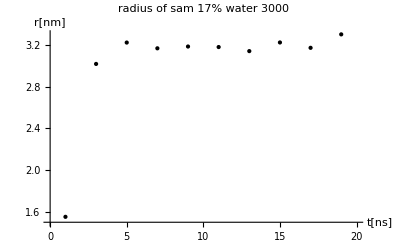

```mathematica
r173000={{1,1.55206},{3,3.01827},{5,3.22327},{7,3.16801},{9,3.18525},{11,3.18015},{13,3.14111},{15,3.2241},{17,3.17274},{19,3.30175}}
model=a+b Exp[-t/c];
fit=FindFit[r173000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r173000],FrameLabel->{"t[ns]","r[nm]"},PlotRange->{1.5,3.3},PlotLabel->"radius of sam 17% water 3000"]
```

```mathematica
t={1,3,5,7,9,11,13,15,17,19}
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
t51t=Thread[{t,t51000}];
t52t=Thread[{t,t52000}];
t53t=Thread[{t,t53000}]
t54t=Thread[{t,t54000}];
t111t=Thread[{t,t111000}];
t112t=Thread[{t,t112000}];
t113t=Thread[{t,t113000}];
t114t=Thread[{t,t114000}];
t171t=Thread[{t,t171000}];
t172t=Thread[{t,t172000}];
t173t=Thread[{t,t173000}];
t174t=Thread[{t,t174000}];
r51t=Thread[{t,r51000}];
r52t=Thread[{t,r52000}];
r53t=Thread[{t,r53000}];
r54t=Thread[{t,r54000}];
r111t=Thread[{t,r111000}];
r112t=Thread[{t,r112000}];
r113t=Thread[{t,r113000}];
r114t=Thread[{t,r114000}];
r171t=Thread[{t,r171000}];
r172t=Thread[{t,r172000}];
r173t=Thread[{t,r173000}];
r174t=Thread[{t,r174000}];
```

{{1,137.33},{3,135.966},{5,34.1683},{7,133.254},{9,135.061},{11,135.669},{13,135.188},{15,135.008},{17,137.818},{19,135.119}}

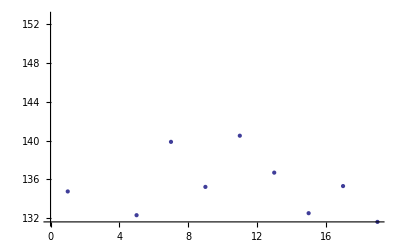

General::ivar: 1 is not a valid variable.

FindFit[{{1,134.75},{3,170.465},{5,132.3},{7,139.865},{9,135.219},{11,140.499},{13,136.69},{15,132.506},{17,135.303},{19,131.609}},a,{a},{1,3,5,7,9,11,13,15,17,19}]

General::ivar: 1 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, 134.75}, {3, 170.465}, {5, 132.3}, {7, 139.865}, {9, 135.219}, {11, 140.499}, {13, 136.69}, {15, 132.506}, {17, 135.303}, {19, 131.609}}, a, {a}, {1, 3, 5, 7, 9, 11, 13, 15, 17, 19}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::nonopt: Options expected (instead of ListPlot[t51t]) beyond position 3 in Plot[modelf[t], {t, 0, 20}, Epilog → Point/@t51t, AxesLabel → {"t[ns]", "r[nm]"}, PlotRange → {130, 155}, ListPlot[t51t], PlotLabel → "radius of sam 5% water 4000"]. An option must be a rule or a list of rules.

Show::gtype: Plot is not a type of graphics.

```mathematica
ListPlot[t51t]
model=a;
fit=FindFit[t51t,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Show[Plot[modelf[t],{t,0,20},Epilog->Map[Point,t51t],FrameLabel->{"t[ns]","r[nm]"},PlotRange->{130,155},ListPlot[t51t],PlotLabel->"radius of sam 5% water 4000"]]
```

```mathematica
Show[Plot[modelf[t],{t,0,20},Epilog->Point/@t51t,FrameLabel->{"t[ns]","r[nm]"},PlotRange->{130,155},ListPlot[t51t],PlotLabel->"radius of sam 5% water 4000"]]
```

```mathematica
model = a
fit51t=FindFit[t51t,model,{a},x]
fit52t=FindFit[t52t,model,{a},x]
fit53t=FindFit[t53t,model,{a},x]
fit54t=FindFit[t54t,model,{a},x]
fit111t=FindFit[t111t,model,{a},x]
fit112t=FindFit[t112t,model,{a},x]
fit113t=FindFit[t113t,model,{a},x]
fit114t=FindFit[t114t,model,{a},x]
fit171t=FindFit[t171t,model,{a},x]
fit172t=FindFit[t172t,model,{a},x]
fit173t=FindFit[t173t,model,{a},x]
fit174t=FindFit[t174t,model,{a},x]
fit51r=FindFit[r51t,model,{a},x]
fit52r=FindFit[r52t,model,{a},x]
fit53r=FindFit[r53t,model,{a},x]
fit54r=FindFit[r54t,model,{a},x]
fit111r=FindFit[r111t,model,{a},x]
fit112r=FindFit[r112t,model,{a},x]
fit113r=FindFit[r113t,model,{a},x]
fit114r=FindFit[r114t,model,{a},x]
fit171r=FindFit[r171t,model,{a},x]
fit172r=FindFit[r172t,model,{a},x]
fit173r=FindFit[r173t,model,{a},x]
fit174r=FindFit[r174t,model,{a},x]
```

a

{a→138.921}

{a→134.536}

{a→125.458}

{a→130.942}

{a→114.954}

{a→115.581}

{a→114.815}

{a→118.133}

{a→107.63}

{a→100.837}

{a→102.835}

{a→103.459}

{a→1.33843}

{a→1.83098}

{a→2.04141}

{a→2.4807}

{a→2.01595}

{a→2.46635}

{a→2.85665}

{a→3.06861}

{a→2.19106}

{a→2.93485}

{a→3.32979}

{a→3.77727}

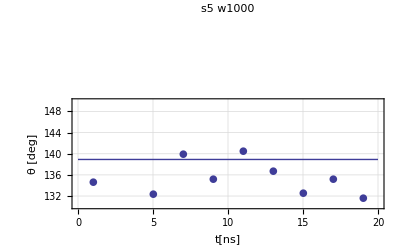

```mathematica
Show[Plot[138.92059118720002,{x,0,20}],ListPlot[t51t,PlotMarkers->{●,10}],PlotRange->{{0,20},{130,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w1000"]
```

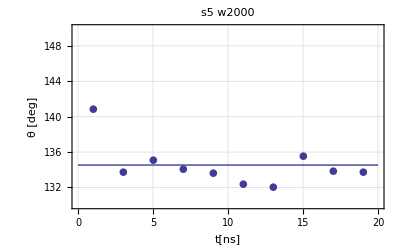

```mathematica
Show[Plot[134.53625385520002,{x,0,20}],ListPlot[t52t,PlotMarkers->{●,10}],PlotRange->{{0,20},{130,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w2000"]
```

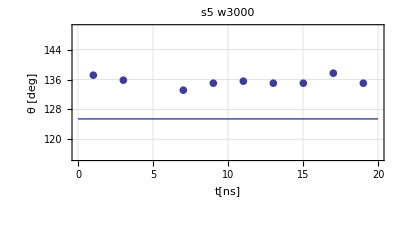

```mathematica
Show[Plot[125.45823807340001,{x,0,20}],ListPlot[t53t,PlotMarkers->{●,10}],PlotRange->{{0,20},{115,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w3000"]
```

```mathematica
Mean[t51t]
Mean[t52t]
Mean[t53t]
Mean[t54t]
Mean[t171t]
Mean[t172t]
Mean[t173t]
Mean[t174t]
```

{10,138.921}

{10,134.536}

{10,125.458}

{10,130.942}

{10,107.63}

{10,100.837}

{10,102.835}

{10,103.459}

```mathematica
t510002=input[[{4,5,6,7,8,9,10},1]];
t520002=input[[{15,16,17,18,19,20,21},1]];
t530002=input[[{26,27,28,29,30,31,32},1]];
t540002=input[[{37,38,39,40,41,42,43},1]];
t1110002=input[[{48,49,50,51,52,53,54},1]];
t1120002=input[[{59,60,61,62,63,64,65},1]];
t1130002=input[[{70,71,72,73,74,75,76},1]];
t1140002=input[[{81,82,83,84,85,86,87},1]];
t1710002=input[[{92,93,94,95,96,97,98},1]];
t1720002=input[[{103,104,105,106,107,108,109},1]];
t1730002=input[[{114,115,116,117,118,119,120},1]];
t1740002=input[[{125,126,127,128,129,130,131},1]];
```

```mathematica
r510002=input[[{4,5,6,7,8,9,10},2]];
r520002=input[[{15,16,17,18,19,20,21},2]];
r530002=input[[{26,27,28,29,30,31,32},2]];
r540002=input[[{37,38,39,40,41,42,43},2]];
r1110002=input[[{48,49,50,51,52,53,54},2]];
r1120002=input[[{59,60,61,62,63,64,65},2]];
r1130002=input[[{70,71,72,73,74,75,76},2]];
r1140002=input[[{81,82,83,84,85,86,87},2]];
r1710002=input[[{92,93,94,95,96,97,98},2]];
r1720002=input[[{103,104,105,106,107,108,109},2]];
r1730002=input[[{114,115,116,117,118,119,120},2]];
r1740002=input[[{125,126,127,128,129,130,131},2]];
```

```mathematica
t2={7,9,11,13,15,17,19}
```

{7,9,11,13,15,17,19}

```mathematica
t51t2=Thread[{t2,t510002}];
t52t2=Thread[{t2,t520002}];
t53t2=Thread[{t2,t530002}]
t54t2=Thread[{t2,t540002}];
t111t2=Thread[{t2,t1110002}];
t112t2=Thread[{t2,t1120002}];
t113t2=Thread[{t2,t1130002}];
t114t2=Thread[{t2,t1140002}];
t171t2=Thread[{t2,t1710002}];
t172t2=Thread[{t2,t1720002}];
t173t2=Thread[{t2,t1730002}];
t174t2=Thread[{t2,t1740002}];
r51t2=Thread[{t2,r510002}];
r52t2=Thread[{t2,r520002}];
r53t2=Thread[{t2,r530002}];
r54t2=Thread[{t2,r540002}];
r111t2=Thread[{t2,r1110002}];
r112t2=Thread[{t2,r1120002}];
r113t2=Thread[{t2,r1130002}];
r114t2=Thread[{t2,r1140002}];
r171t2=Thread[{t2,r1710002}];
r172t2=Thread[{t2,r1720002}];
r173t2=Thread[{t2,r1730002}];
r174t2=Thread[{t2,r1740002}];
```

{{7,133.254},{9,135.061},{11,135.669},{13,135.188},{15,135.008},{17,137.818},{19,135.119}}

```mathematica
model2 = a2
fit51t2=FindFit[t51t2,model2,{a2},x]
fit52t2=FindFit[t52t2,model2,{a2},x]
fit53t2=FindFit[t53t2,model2,{a2},x]
fit54t2=FindFit[t54t2,model2,{a2},x]
fit111t2=FindFit[t111t2,model2,{a2},x]
fit112t2=FindFit[t112t2,model2,{a2},x]
fit113t2=FindFit[t113t2,model2,{a2},x]
fit114t2=FindFit[t114t2,model2,{a2},x]
fit171t2=FindFit[t171t2,model2,{a2},x]
fit172t2=FindFit[t172t2,model2,{a2},x]
fit173t2=FindFit[t173t2,model2,{a2},x]
fit174t2=FindFit[t174t2,model2,{a2},x]
fit51r2=FindFit[r51t2,model2,{a2},x]
fit52r2=FindFit[r52t2,model2,{a2},x]
fit53r2=FindFit[r53t2,model2,{a2},x]
fit54r2=FindFit[r54t2,model2,{a2},x]
fit111r2=FindFit[r111t2,model2,{a2},x]
fit112r2=FindFit[r112t2,model2,{a2},x]
fit113r2=FindFit[r113t2,model2,{a2},x]
fit114r2=FindFit[r114t2,model2,{a2},x]
fit171r2=FindFit[r171t2,model2,{a2},x]
fit172r2=FindFit[r172t2,model2,{a2},x]
fit173r2=FindFit[r173t2,model2,{a2},x]
fit174r2=FindFit[r174t2,model2,{a2},x]
```

a2

{a2→135.956}

{a2→133.647}

{a2→135.303}

{a2→128.841}

{a2→113.094}

{a2→115.639}

{a2→113.463}

{a2→117.564}

{a2→107.286}

{a2→99.5336}

{a2→100.893}

{a2→101.56}

{a2→1.44281}

{a2→1.84458}

{a2→2.00998}

{a2→2.51723}

{a2→2.07234}

{a2→2.42059}

{a2→2.8342}

{a2→2.92646}

{a2→2.18476}

{a2→2.9141}

{a2→3.27517}

{a2→3.58261}

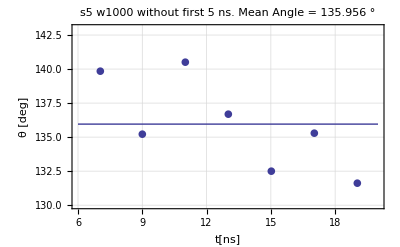

```mathematica
Show[Plot[{model2/.fit51t2},{x,6,20}],ListPlot[t51t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{130,143}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w1000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit51t2]<>" °"]
```

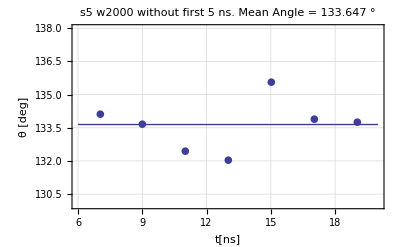

```mathematica
Show[Plot[{model2/.fit52t2},{x,6,20}],ListPlot[t52t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{130,138}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w2000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit52t2]<>" °"]
```

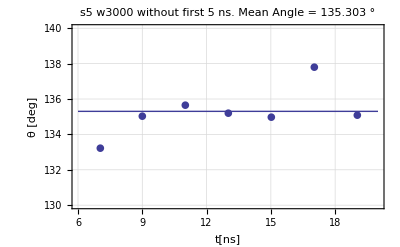

```mathematica
Show[Plot[{model2/.fit53t2},{x,6,20}],ListPlot[t53t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{130,140}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w3000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit53t2]<>" °"]
```

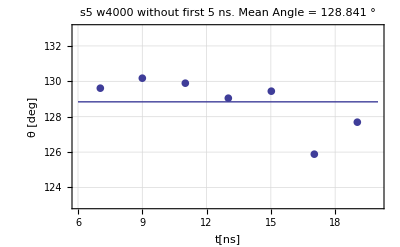

```mathematica
Show[Plot[{model2/.fit54t2},{x,6,20}],ListPlot[t54t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{123,133}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s5 w4000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit54t2]<>" °"]
```

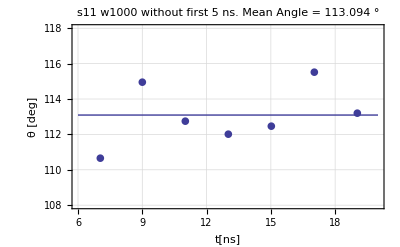

```mathematica
Show[Plot[{model2/.fit111t2},{x,6,20}],ListPlot[t111t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{108,118}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s11 w1000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit111t2]<>" °"]
```

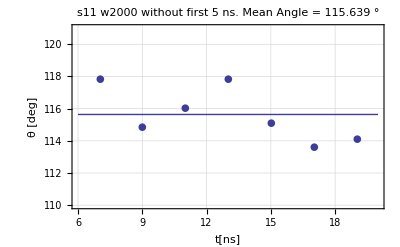

```mathematica
Show[Plot[{model2/.fit112t2},{x,6,20}],ListPlot[t112t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{110,121}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s11 w2000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit112t2]<>" °"]
```

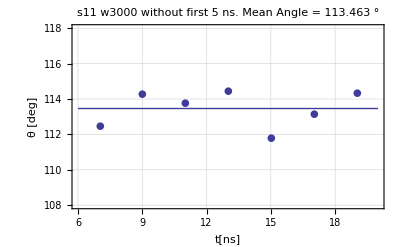

```mathematica
Show[Plot[{model2/.fit113t2},{x,6,20}],ListPlot[t113t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{108,118}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s11 w3000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit113t2]<>" °"]
```

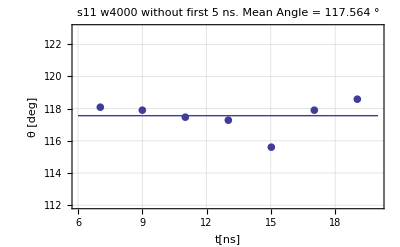

```mathematica
Show[Plot[{model2/.fit114t2},{x,6,20}],ListPlot[t114t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{112,123}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s11 w4000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit114t2]<>" °"]
```

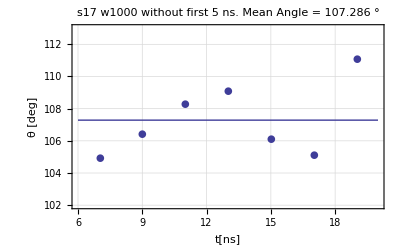

```mathematica
Show[Plot[{model2/.fit171t2},{x,6,20}],ListPlot[t171t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{102,113}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s17 w1000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit171t2]<>" °"]
```

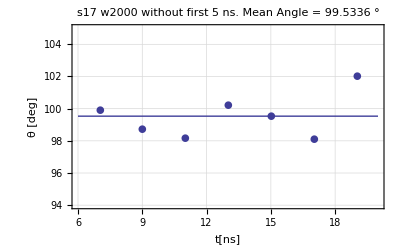

```mathematica
Show[Plot[{model2/.fit172t2},{x,6,20}],ListPlot[t172t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{94,105}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s17 w2000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit172t2]<>" °"]
```

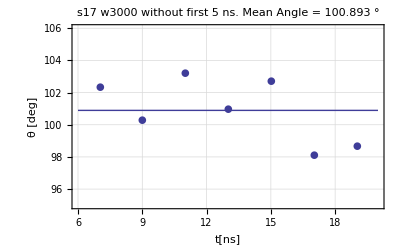

```mathematica
Show[Plot[{model2/.fit173t2},{x,6,20}],ListPlot[t173t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{95,106}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s17 w3000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit173t2]<>" °"]
```

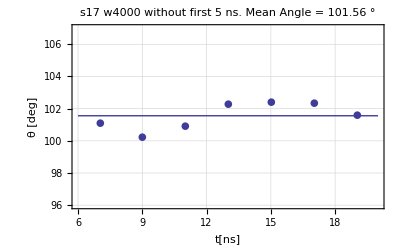

```mathematica
Show[Plot[{model2/.fit174t2},{x,6,20}],ListPlot[t174t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{96,107}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","θ [deg]"},PlotLabel->"s17 w4000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit174t2]<>" °"]
```

```mathematica
lm=LinearModelFit[t174t2,x,x]
 lm["ParameterTable"]
```

FittedModel[99.8978+0.127831 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 99.8978 | 0.876903 | 113.921 | 9.88381×10^-10
x | 0.127831 | 0.0644712 | 1.98276 | 0.10421

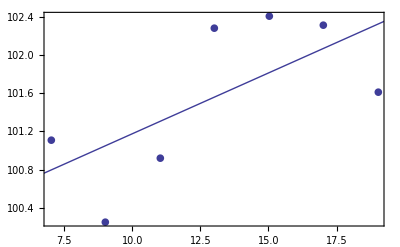

```mathematica
Show[ListPlot[t174t2,PlotMarkers->{●,10}],Plot[lm[x],{x,6,20},PlotRange->{{6,20},{90,107}}],Frame->True]
```

```mathematica
StandardDeviation[t51t2]
StandardDeviation[t52t2]
StandardDeviation[t53t2]
StandardDeviation[t54t2]
StandardDeviation[t111t2]
StandardDeviation[t112t2]
StandardDeviation[t113t2]
StandardDeviation[t114t2]
StandardDeviation[t171t2]
StandardDeviation[t172t2]
StandardDeviation[t173t2]
StandardDeviation[t174t2]
```

{2 √(14/3),3.37188}

{2 √(14/3),1.16148}

{2 √(14/3),1.3449}

{2 √(14/3),1.52741}

{2 √(14/3),1.67423}

{2 √(14/3),1.68971}

{2 √(14/3),1.03012}

{2 √(14/3),0.945955}

{2 √(14/3),2.28148}

{2 √(14/3),1.38518}

{2 √(14/3),1.99367}

{2 √(14/3),0.832449}

```mathematica
StandardDeviation[r51t2]
StandardDeviation[r52t2]
StandardDeviation[r53t2]
StandardDeviation[r54t2]
StandardDeviation[r111t2]
StandardDeviation[r112t2]
StandardDeviation[r113t2]
StandardDeviation[r114t2]
StandardDeviation[r171t2]
StandardDeviation[r172t2]
StandardDeviation[r173t2]
StandardDeviation[r174t2]
```

{2 √(14/3),0.105932}

{2 √(14/3),0.0645946}

{2 √(14/3),0.073815}

{2 √(14/3),0.0917469}

{2 √(14/3),0.0308345}

{2 √(14/3),0.0997171}

{2 √(14/3),0.0598617}

{2 √(14/3),0.0421715}

{2 √(14/3),0.0626281}

{2 √(14/3),0.0800946}

{2 √(14/3),0.145451}

{2 √(14/3),0.0800074}

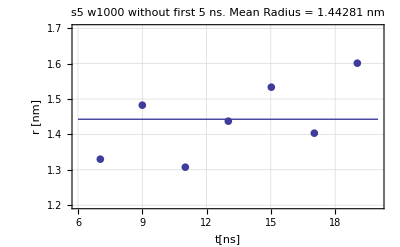

```mathematica
Show[Plot[{model2/.fit51r2},{x,6,20}],ListPlot[r51t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.2,1.7}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s5 w1000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit51r2]<>" nm"]
```

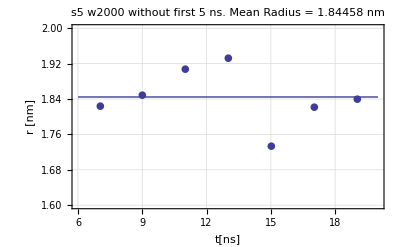

```mathematica
Show[Plot[{model2/.fit52r2},{x,6,20}],ListPlot[r52t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.6,2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s5 w2000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit52r2]<>" nm"]
```

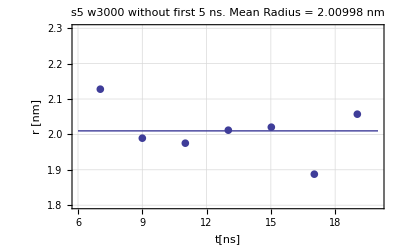

```mathematica
Show[Plot[{model2/.fit53r2},{x,6,20}],ListPlot[r53t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.8,2.3}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s5 w3000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit53r2]<>" nm"]
```

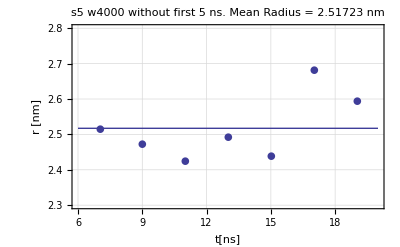

```mathematica
Show[Plot[{model2/.fit54r2},{x,6,20}],ListPlot[r54t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.3,2.8}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s5 w4000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit54r2]<>" nm"]
```

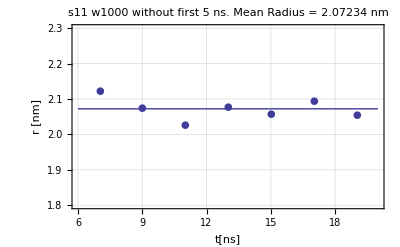

```mathematica
Show[Plot[{model2/.fit111r2},{x,6,20}],ListPlot[r111t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.8,2.3}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s11 w1000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit111r2]<>" nm"]
```

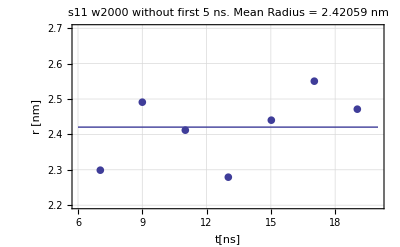

```mathematica
Show[Plot[{model2/.fit112r2},{x,6,20}],ListPlot[r112t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.2,2.7}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s11 w2000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit112r2]<>" nm"]
```

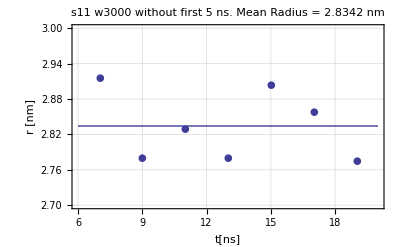

```mathematica
Show[Plot[{model2/.fit113r2},{x,6,20}],ListPlot[r113t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.7,3.0}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s11 w3000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit113r2]<>" nm"]
```

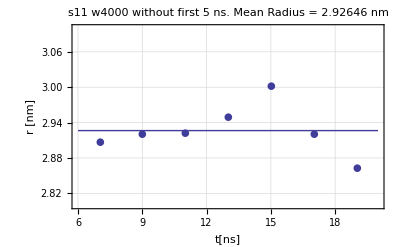

```mathematica
Show[Plot[{model2/.fit114r2},{x,6,20}],ListPlot[r114t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.8,3.1}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s11 w4000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit114r2]<>" nm"]
```

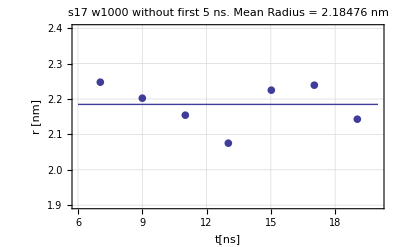

```mathematica
Show[Plot[{model2/.fit171r2},{x,6,20}],ListPlot[r171t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.9,2.4}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s17 w1000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit171r2]<>" nm"]
```

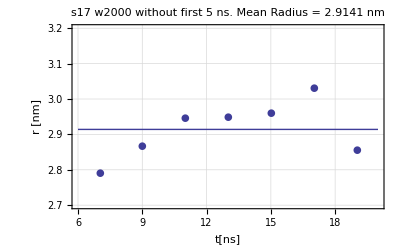

```mathematica
Show[Plot[{model2/.fit172r2},{x,6,20}],ListPlot[r172t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.7,3.2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s17 w2000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit172r2]<>" nm"]
```

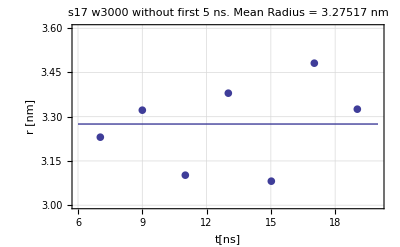

```mathematica
Show[Plot[{model2/.fit173r2},{x,6,20}],ListPlot[r173t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{3.0,3.6}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s17 w3000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit173r2]<>" nm"]
```

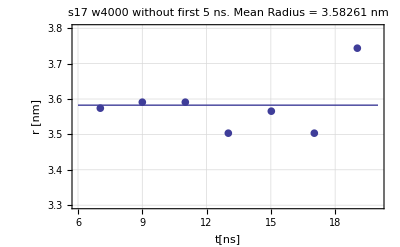

```mathematica
Show[Plot[{model2/.fit174r2},{x,6,20}],ListPlot[r174t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{3.3,3.8}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"t[ns]","r [nm]"},PlotLabel->"s17 w4000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit174r2]<>" nm"]
```